Autor:           		Jhordan Silveira de Borba
E-mail:          		sbjhordan@gmail.com
Site:            		https://sites.google.com/view/jdan/
Modelo original: 	Oscillations in SIRS model with distributed delays
Link:           		 https://arxiv.org/abs/1409.0024

```mathematica
Com atraso antes de 0
max=400;b=0.8;ti=5;to=20;
ci1=NDSolve[{
s1'[t]==-b*s1[t]*i1[t],
i1'[t]==+b*s1[t]*i1[t],
s1[0]==0.99,i1[0]==0.01},
{s1,i1},{t,0,ti}];
ci2=NDSolve[{
s2'[t]==-b*s2[t]*i2[t],
i2'[t]==+b*s2[t]*i2[t]-b*s2[t-ti]*i2[t-ti],
s2[t/;t≤0]==s1[t+ti]/.ci1,i2[t/;t≤0]==i1[t+ti]/.ci1},
{s2,i2},{t,-ti,to-ti}];
sol=NDSolve[{
s3'[t]==-b*s3[t]*i3[t],
i3'[t]==+b*s3[t]*i3[t]-b*s3[t-ti]*i3[t-ti],
s3[t/;t≤ti]==s1[t]/.ci1,i3[t/;t≤ti]==i2[t]/.ci2},
{s3,i3},{t,0,to}];
```

```mathematica
Com atraso depois de 0
```

```mathematica
max=400;b=0.8;ti=5;to=20;
ci1=NDSolve[{
s1'[t]==-b*s1[t]*i1[t],
i1'[t]==+b*s1[t]*i1[t],
s1[0]==0.99,i1[0]==0.01},
{s1,i1},{t,0,ti}];
(*Plot[{s1[t]/.ci1,i1[t]/.ci1},{t,0,ti},PlotRange->{0,1}]*)
```

```mathematica
ci2=NDSolve[{
s2'[t]==-b*s2[t]*i2[t],
i2'[t]==+b*s2[t]*i2[t]-b*s2[t-ti]*i2[t-ti],
s2[t/;t≤ti]==s1[t]/.ci1,i2[t/;t≤ti]==i1[t]/.ci1},
{s2,i2},{t,0,to}];
(*Plot[{s2[t]/.ci2,i2[t]/.ci2},{t,0,to},PlotRange->{0,1}]*)
```

```mathematica
sol=NDSolve[{
s'[t]==-b*s[t]*i[t]+b*s[t-to]*i[t-to],
i'[t]==+b*s[t]*i[t]-b*s[t-ti]*i[t-ti],
s[t/;t≤to]==s2[t]/.ci2,i[t/;t≤to]==i2[t]/.ci2},
{s,i},{t,0,300}];
```

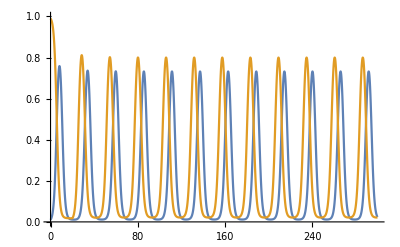

```mathematica
Plot[{i[t]/.sol,s[t]/.sol},{t,0,300},PlotRange->{0.,1.}]
```

O sistema evolui das condições iniciais até equilibrar b*s[t]*i[t]=b*s[t-ti]*i[t-ti], porém como isso pode ser alcançado para basicamente qualquer par de valore (s[t],i[t]) depende das condições iniciais quando é que esse equilíbrio vai ser atingido. Então quando o equilíbrio é atingido, há a existência de ‘infectados’ permanentes.

## Sem atraso

```mathematica
tmax=400;b=0.4;ti=5;tr=50;
sol=NDSolve[{
s'[t]==-b*s[t]*i[t]+r[t]/tr,
i'[t]==+b*s[t]*i[t]-i[t]/ti,
r'[t]==i[t]/ti-r[t]/tr,
(*s[0]==1/(b*ti),i[0]==(b*ti-1)/(b*to),r[0]==1-1/(b*ti)-(b*ti-1)/(b*to)},*)
s[0]==0.5,i[0]==0.5,r[0]==0},
{s,i,r},{t,0,500}];
```

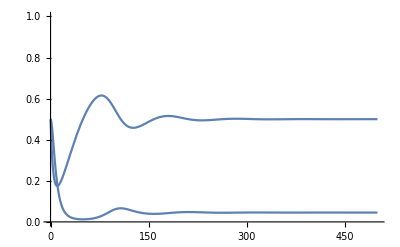

```mathematica
Plot[{i[t]/.sol,s[t]}/.sol,{t,0,500},PlotRange->{0.,1.}]
```

```mathematica
{{b*s[10]*i[10],i[10]/ti},{b*s[10]*i[10]*ti,i[10]},i[10]-b*s[10]*i[10]*ti}/.sol
```

{{{0.00909091,0.00909091},{0.0454545,0.0454545},0.}}

Observações:
Neste caso, o sistema busca o equilíbrio para equilibrar os novos casos de infectados c[_t]:= b*s[t]*i[t] com a recuperação i[t]/ti. Nesse caso independe das condições iniciais, e no equilíbrio acontee que todos os novos casos também são oriundo dos infectados c[t] durante o tempo ti.

```mathematica
d[t_+ti]:=s1[t]/.ci1
d[1]
```

d[1]

```mathematica
]
```

a[0]